```mathematica
(* Convenience palette colours *)
blue   = RGBColor[0.122, 0.467, 0.706];
orange = RGBColor[1.000, 0.498, 0.055];
green  = RGBColor[0.173, 0.627, 0.173];
red    = RGBColor[0.839, 0.153, 0.157];
purple = RGBColor[0.580, 0.404, 0.741];
```

The numerical methods to be implemented here are:
- Euler’s method
y_(n+1)=y_n+h*f(x_n,y_n)
- Heun’s method/Improved Euler’s method
y_(n+1)=y_n+h (f(x_n,y_n)+f(x_(n+1),y_n+hf(x_n,y_n)))/2
- Fourth order Runge-Kutta method
y_(n+1)=y_n+h (k_1+2 k_2+2 k_3+k_4)/6;
 k_1=f(x_n,y_n);k_2=f(x_n+h/2,y_n+h/2 k_1);k_3=f(x_n+h/2,y_n+h/2 k_2);k_4=f(x_n+h,y_n+hk_3)

```mathematica
(*Euler Step*)
(* Forward Euler — first-order, O(h) local error *)
eulerStep[f_, x_, t_, h_] := x + h * f[x, t]

(*Improved Euler Step*)
(* Heun's method/Improved Euler — second-order, O(h^2) local error *)
heunStep[f_, x_, t_, h_] := x + (h/2)(f[x, t]+ f[x+h*f[x,t],t+ h/2 ])

(*Runge-Kutta 4 Step*)
(* Classical RK4 — fourth-order, O(h^4) local error *)
rk4Step[f_, x_, t_, h_] :=
  Module[{k1, k2, k3, k4},
    k1 = f[x,t];
    k2 = f[x + h k1/2,  t + h/2 ];
    k3 = f[x + h k2/2,  t + h/2 ];
    k4 = f[x + h k3,    t + h   ];
    x + (h/6)(k1 + 2 k2 + 2 k3 + k4)
  ]
(* Generic driver: applies stepFn repeatedly over a uniform grid *)
integrate[stepFn_, f_, x0_, {t0_, t1_}, h_] :=
  Module[{tGrid, xs, x},
    tGrid = Range[t0, t1, h];
    x = x0;
    xs = Reap[
      Sow[{t0, x}];
      Do[x = stepFn[f, x, tGrid[[i]], h];
        Sow[{tGrid[[i + 1]], x}],
        {i, 1, Length[tGrid] - 1}]
    ][[2, 1]];
    xs
  ]

eulerSolve[f_, x0_, tSpan_, h_] := integrate[eulerStep, f, x0, tSpan, h]
heunSolve[f_, x0_, tSpan_, h_] := integrate[heunStep, f, x0, tSpan, h]
rk4Solve[f_,   x0_, tSpan_, h_] := integrate[rk4Step,   f, x0, tSpan, h]
```

## Logistic Equation

A mathematical model used to describe population growth that account for limited resources is formulated through the logistic equation:
															dP/dt=rP(1-P/K)
where P is the pullulation, r is the growth rate and K is the carrying capacity.

For this problem, suppose the initial conditions:
r = 1.5   (growth rate)
K = 10.0;  (carrying capacity)
P[0] = 0.5;  (initial population)
What will be the population after 8 time units?
															T[8]=?

```mathematica
(*Parameters*)
rLog=1.5;   (*growth rate*)
KLog=10.0;  (*carrying capacity*)
x0Log=0.5;  (*initial population*)
tSpanLog={0.0,8.0};
hLog=0.2;

(*RHS function*)
logisticF[x_,t_]:=rLog*x*(1-x/KLog)

(*Exact (closed-form) solution*)
logisticExact[t_]:=KLog/(1+((KLog-x0Log)/x0Log) Exp[-rLog t])

Print["Logistic equation: dx/dt = ",rLog," x (1 - x/",KLog,")"]
Print["x(0) = ",x0Log,",  t in ",tSpanLog]
```

Logistic equation: dx/dt = 1.5 x (1 - x/10.)

x(0) = 0.5,  t in {0.,8.}

=== Logistic Equation — Error & Timing ===

Method | Max |Error| | Timing (s) | Result P[8]
Euler | 6.118×10^-1 | 0.000285 | 9.999626
Euler | 5.231×10^-2 | 0.000361 | 9.998630
RK4 | 1.581×10^-4 | 0.000720 | 9.998832
NDSolve | 9.124×10^-7 | 0.006039 | 9.998833

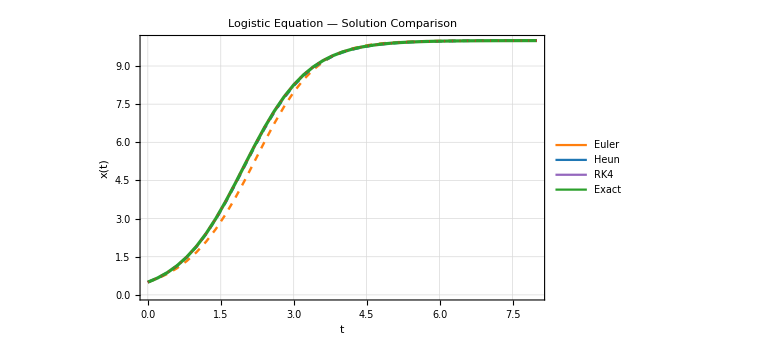

```mathematica
(*Solve with all three manual methods*)
{tEulerLog,eulerLog}=AbsoluteTiming[eulerSolve[logisticF,x0Log,tSpanLog,hLog]];
{tHeunLog,heunLog}=AbsoluteTiming[heunSolve[logisticF,x0Log,tSpanLog,hLog]];
{tRK4Log,rk4Log}=AbsoluteTiming[rk4Solve[logisticF,x0Log,tSpanLog,hLog]];
(*Built-in NDSolve*)
{tNDLog,ndLog}=AbsoluteTiming[NDSolve[{x'[t]==logisticF[x[t],t],x[0]==x0Log},x,{t,tSpanLog[[1]],tSpanLog[[2]]},MaxStepSize->hLog]];
ndLogFn=x/. ndLog[[1]];  (*interpolating function*)

(*Exact reference on same grid*)
tGridLog=eulerLog[[All,1]];
exactLog={#,logisticExact[#]}&/@tGridLog;

(*Error analysis*)
(*Max absolute error vs closed-form solution*)
errEulerLog=Max[Abs[eulerLog[[All,2]]-exactLog[[All,2]]]];
errHeunLog=Max[Abs[heunLog[[All,2]]-exactLog[[All,2]]]];
errRK4Log=Max[Abs[rk4Log[[All,2]]-exactLog[[All,2]]]];
errNDLog=Max[Abs[(ndLogFn/@tGridLog)-exactLog[[All,2]]]];

errTable=Grid[{{Style["Method",Bold,12],Style["Max |Error|",Bold,12],Style["Timing (s)",Bold,12],Style["Result P[8]",Bold,12]},{"Euler",ScientificForm[errEulerLog,4],NumberForm[tEulerLog,{5,6}],NumberForm[eulerLog[[-1]][[2]],{8,6}]},{"Euler",ScientificForm[errHeunLog,4],NumberForm[tHeunLog,{5,6}],NumberForm[heunLog[[-1]][[2]],{8,6}]},{"RK4",ScientificForm[errRK4Log,4],NumberForm[tRK4Log,{5,6}],NumberForm[rk4Log[[-1]][[2]],{8,6}]},{"NDSolve",ScientificForm[errNDLog,4],NumberForm[tNDLog,{5,6}],NumberForm[(ndLogFn/@tGridLog)[[-1]],{8,6}]}},Frame->All,Background->{None,{DarkBlue,None,None,None}},Spacings->{2,1}];

Print["=== Logistic Equation — Error & Timing ==="]
Print[errTable]
(*Solution plot*)
logisticPlot=Show[
ListLinePlot[{eulerLog,heunLog,rk4Log,exactLog},
PlotStyle->{Directive[Dashed,orange,Thickness[0.003]],
Directive[Dashed,blue,Thickness[0.003]],
Directive[Dashed,purple,Thickness[0.003]],
Directive[green,Thickness[0.004]]},PlotLegends->Placed[LineLegend[{orange,blue,purple,green},{"Euler","Heun","RK4","Exact"},LegendMarkerSize->25],{Right,Bottom}],PlotRange->All,FrameLabel->{"t","x(t)"},PlotLabel->Style["Logistic Equation — Solution Comparison",14,Bold],GridLines->Automatic,GridLinesStyle->LightGray,Frame->True,ImageSize->Large],
(*NDSolve interpolated curve*)
Plot[ndLogFn[t],{t,tSpanLog[[1]],tSpanLog[[2]]},PlotStyle->Directive[red,Dotted,Thickness[0.003]]]]
```

{{0.4,1.17419,0.1815,0.00215062},{0.2,0.611771,0.0523092,0.000158127},{0.1,0.309776,0.0141308,0.0000107401},{0.05,0.155368,0.00367633,7.00712×10^-7},{0.02,0.0622283,0.000602781,1.83963×10^-8},{0.01,0.031127,0.000151946,1.15949×10^-9}}

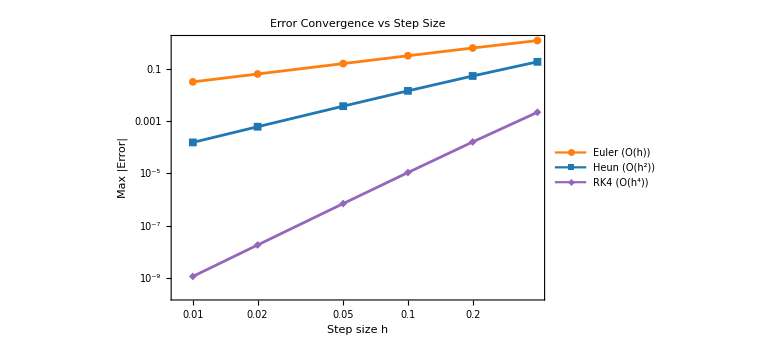

```mathematica
(*Error convergence plot  (how error scales with h)*)
hValues = {0.4, 0.2, 0.1, 0.05, 0.02, 0.01};

errorConvergence = Table[
  Module[{eul,heunsol, rk4sol, exRef, tg},
    eul    = eulerSolve[logisticF, x0Log, tSpanLog, h];
heunsol= heunSolve[logisticF, x0Log, tSpanLog, h];
    rk4sol = rk4Solve[logisticF,   x0Log, tSpanLog, h];
    tg     = eul[[All, 1]];
    exRef  = logisticExact /@ tg;
    {h,
     Max[Abs[eul[[All,2]]    - exRef]],
Max[Abs[heunsol[[All,2]]    - exRef]],
     Max[Abs[rk4sol[[All,2]] - exRef]]}
  ],{h, hValues}
]
convergencePlot = ListLogLogPlot[
  {errorConvergence[[All, {1, 2}]],
   errorConvergence[[All, {1, 3}]],
errorConvergence[[All, {1, 4}]]},
  Joined -> True,
  PlotMarkers -> {Automatic, 8},
  PlotStyle  -> {orange, blue, purple},
  PlotLegends -> LineLegend[{orange, blue, purple}, {"Euler (O(h))", "Heun (O(h^2))", "RK4 (O(h^4))"},
                             LegendMarkerSize -> 20],
  FrameLabel  -> {"Step size h", "Max |Error|"},
  PlotLabel  -> Style["Error Convergence vs Step Size", 14, Bold],
  GridLines  -> Automatic,
  Frame -> True,
  ImageSize -> Large
]
```

## Stefan’s Law

Following Stefan’s law for radiation, absolute temperature T of a given body, cooling in a medium with absolute constant temperature T_m is given by:
															dT/dt=k(T^4-T_m^4)
where k is a proportionality constant dependent on the surface area, the emisivity of the material and the Stefan-Boltzmann constant. 
Stefan’s law can be applied to a greater temperature range than Newton’s law for cooling bodies.

For this problem, suppose a hot body with initial conditions:
T_m=20 K (-253.15 °C as medium constant)
T[0]=300 K (26.85 °C as initial body temperature)
k=-10^-7
Time is measured in minutes.
What temperature will the body have after 30 minutes?
															T[30]=?
Since this equation does not have an exact solution, solving with NDSolve method is set as the reference solution.

```mathematica
Tm=20;k=-10^-7;
x0Temp=300;tSpanTemp={0,30};hTemp=0.01;
TempF[x_,t_]:=k(x^4-Tm^4)
Print["Stefan's Law: dT/dt = ",k," (T^4-",Tm,"^4)"]
Print["T(0) = ",x0Temp,",  t in ",tSpanTemp]
```

Stefan's Law: dT/dt = -1/10000000 (T^4-20^4)

T(0) = 300,  t in {0,30}

=== Stefan's Law - Error & Timing ===

Method | Max |Error| | Timing (s) | Result T[30](K)
Euler | 1.545 | 0.010658 | 48.195940
Heun | 2.524×10^-2 | 0.020804 | 48.215375
RK4 | 6.702×10^-6 | 0.048935 | 48.215296
NDSolve | Set as reference | 0.001036 | 48.215294

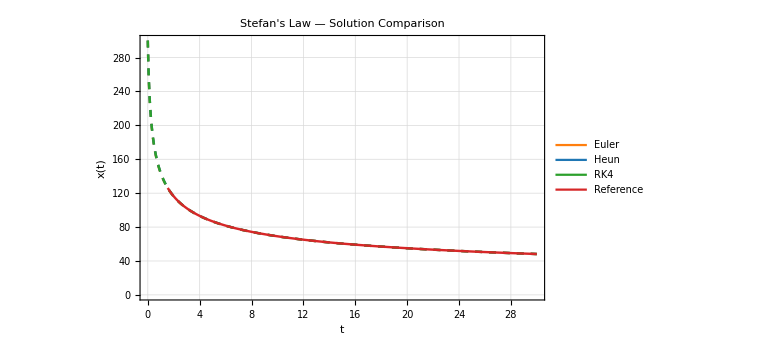

```mathematica
(*Solving the equation*)
{tEulerTemp, eulerTemp}  = AbsoluteTiming[eulerSolve[TempF, x0Temp, tSpanTemp, hTemp]];
{tHeunTemp, heunTemp}  = AbsoluteTiming[heunSolve[TempF, x0Temp, tSpanTemp, hTemp]];
{tRK4Temp,rk4Temp}= AbsoluteTiming[rk4Solve[TempF, x0Temp, tSpanTemp, hTemp]];
(*NDSolve reference*)
{tNDTemp,ndTemp}=AbsoluteTiming[NDSolve[{x'[t]==TempF[x[t],t],x[0]==x0Temp},x,{t,tSpanTemp[[1]],tSpanTemp[[2]]}]];
(*interpolating function*)
ndTempFn=x/. ndTemp[[1]];
(*Error analysis*)
(* Max absolute error vs reference solution *)
ndTempGrid=ndTempFn/@eulerTemp[[All,1]];
errEulerTemp = Max[Abs[eulerTemp[[All, 2]] -ndTempGrid]];
errHeunTemp = Max[Abs[heunTemp[[All, 2]] -ndTempGrid]];
errRK4Temp = Max[Abs[rk4Temp[[All, 2]]   -ndTempGrid]];
errTable=Grid[{{Style["Method",Bold,12],Style["Max |Error|",Bold,12],Style["Timing (s)",Bold,12],Style["Result T[30](K)",Bold,12]},{"Euler",ScientificForm[errEulerTemp,4],NumberForm[tEulerTemp,{5,6}],NumberForm[eulerTemp[[-1]][[2]],{8,6}]},{"Heun",ScientificForm[errHeunTemp,4],NumberForm[tHeunTemp,{5,6}],NumberForm[heunTemp[[-1]][[2]],{8,6}]},{"RK4",ScientificForm[errRK4Temp,4],NumberForm[tRK4Temp,{5,6}],NumberForm[rk4Temp[[-1]][[2]],{8,6}]},{"NDSolve","Set as reference",NumberForm[tNDTemp,{5,6}],NumberForm[ndTempGrid[[-1]],{8,6}]}},Frame->All,Background->{None,{DarkBlue,None,None,None}},Spacings->{2,1}];

Print["=== Stefan's Law - Error & Timing ==="]
Print[errTable]
(*Solution plot*)
logisticPlot = Show[ ListLinePlot[{eulerTemp, heunTemp, rk4Temp},
    PlotStyle -> {
      Directive[Dashed, orange,Thickness[0.003]],
      Directive[Dashed, blue,Thickness[0.003]],
      Directive[Dashed, green,Thickness[0.003]]
    },
    PlotLegends -> Placed[
      LineLegend[{orange, blue, green,red},{"Euler", "Heun", "RK4", "Reference"},LegendMarkerSize -> 25],
      {Right, Top}],
    PlotRange -> All,
    FrameLabel -> {"t", "x(t)"},PlotLabel -> Style["Stefan's Law — Solution Comparison", 14, Bold],
    GridLines -> Automatic,GridLinesStyle -> LightGray,Frame -> True,
    ImageSize -> Large
  ],
(*NDSolve interpolated curve*)
Plot[ndTempFn[t],{t,tSpanTemp[[1]],tSpanTemp[[2]]},PlotStyle->Directive[red,Thickness[0.003]]]
]
```

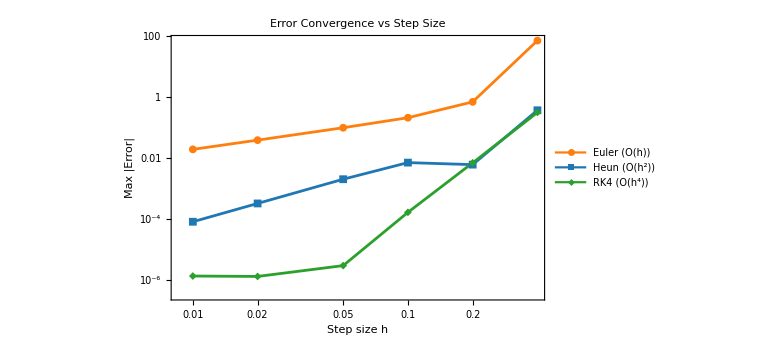

```mathematica
(*Error convergence plot  (how error scales with h)*)
hValues = {0.4, 0.2, 0.1, 0.05, 0.02, 0.01};

errorConvergence = Table[
  Module[{eul, heunsol,rk4sol},
    eul    = eulerSolve[TempF, x0Temp, tSpanTemp, h];
    heunsol = heunSolve[TempF, x0Temp, tSpanTemp, h];
rk4sol = rk4Solve[TempF, x0Temp, tSpanTemp, h];
    {h,
     Max[Abs[eul[[-1]][[2]]-ndTempGrid[[-1]]]],
     Max[Abs[heunsol[[-1]][[2]]-ndTempGrid[[-1]]]],
     Max[Abs[rk4sol[[-1]][[2]]-ndTempGrid[[-1]]]]}
  ],
  {h, hValues}];

convergencePlot = ListLogLogPlot[
  {errorConvergence[[All, {1, 2}]],errorConvergence[[All, {1, 3}]],errorConvergence[[All, {1, 4}]]},
  Joined -> True,
  PlotMarkers -> {Automatic, 8},
  PlotStyle  -> {orange, blue,green},
  PlotLegends -> LineLegend[{orange, blue, green}, {"Euler (O(h))", "Heun (O(h^2))", "RK4 (O(h^4))"},
                             LegendMarkerSize -> 20],
  FrameLabel  -> {"Step size h", "Max |Error|"},PlotLabel  -> Style["Error Convergence vs Step Size", 14, Bold],
  GridLines  -> Automatic,Frame -> True,ImageSize -> Large]
```

## Lotka-Volterra Model (Prey-Predator)

A simple, yet usefull, model to describe the dynamics of two interacting species, generally a prey (x) and a predator (y), is conformed by a pair of first order non-linear coupled differential equations. Proposed by Alfred J. Lotka (1925) and Vito Volterra (1926), it models how the growth rate of the prey depends on its abundance and the predation, while the growth rate of the predator depends on the availability of preys, giving oscilating population cycles:
															dx/dt=α x-β x y
															dy/dt=δ x y-γ y
where α is the maximum prey per capita growth rate, β is the effect of the presence of predators on the prey death rate,  γ is the predator’s per capita death rate, and δ is the effect of the presence of prey on the predator’s growth rate.

For this problem, suppose the initial conditions:
α = 1.0 
β = 0.1
δ = 0.075
γ = 1.5
x[0]= 10.0 (density of preys)
y[0]= 5.0 (density of predators)
What density will the populations have after 30 time units?
															T[30]=?
Since this equation does not have an exact solution, solving with NDSolve method is set as the reference solution.

```mathematica
α = 1.0; β = 0.1; δ = 0.075; γ = 1.5;
xy0LV = {10.0, 5.0};
tSpanLV = {0.0, 30.0};
hLV = 0.05;
(*Vector-valued RHS*)
lvF[xy_,t_]:={α xy[[1]]-β xy[[1]] xy[[2]],
                                δ xy[[1]] xy[[2]]-γ xy[[2]]}
Print["Lotka-Volterra system:"]
Print["  dx/dt = ",α," x - ",β," xy"]
Print["  dy/dt = ",δ," xy - ",γ," y"]
Print["  (x0, y0) = ",xy0LV,",  t in ",tSpanLV]
```

Lotka-Volterra system:

dx/dt = 1. x - 0.1 xy

dy/dt = 0.075 xy - 1.5 y

(x0, y0) = {10.,5.},  t in {0.,30.}

=== Lotka-Volterra - Error & Timing ===

Method | Max ‖Error‖₂ | Timing (s) | Result T[30]
Euler | 7.835×10^1 | 0.003544 | {0.513169,7.560391}
Heun | 2.321×10^-1 | 0.008859 | {40.144780,12.061567}
RK4 | 6.723×10^-5 | 0.018350 | {40.163816,11.924082}
NDSolve | Set as reference | 0.001409 | {40.163799,11.924125}

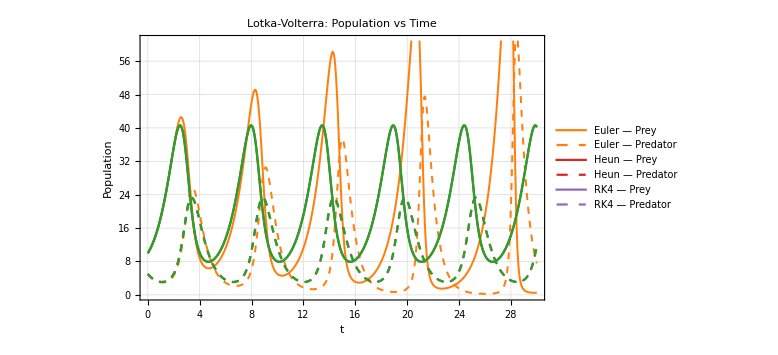

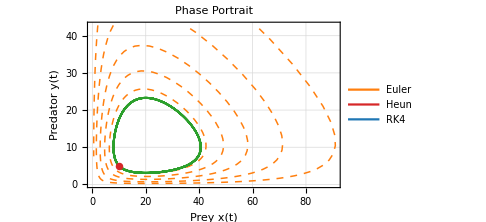

```mathematica
{tEulerLV, eulerLV} = AbsoluteTiming[eulerSolve[lvF, xy0LV, tSpanLV, hLV]];
{tHeunLV, heunLV}  = AbsoluteTiming[heunSolve[lvF, xy0LV, tSpanLV, hLV]];
{tRK4LV,   rk4LV}   = AbsoluteTiming[rk4Solve[lvF,   xy0LV, tSpanLV, hLV]];
(*NDSolve reference*){tNDLV,ndLV}=AbsoluteTiming[NDSolve[{x'[t]==α x[t]-β x[t] y[t],y'[t]==δ x[t] y[t]-γ y[t],x[0]==xy0LV[[1]],y[0]==xy0LV[[2]]},{x,y},{t,tSpanLV[[1]],tSpanLV[[2]]}]];
{xND,yND}={x,y}/. ndLV[[1]];
(*Error vs Reference*)
tGridLV=eulerLV[[All,1]];
errEulerLV=Max[Sqrt[Total[(eulerLV[[All,2]]-({xND[#],yND[#]}&/@tGridLV))^2,{2}]]];
errHeunLV=Max[Sqrt[Total[(heunLV[[All,2]]-({xND[#],yND[#]}&/@tGridLV))^2,{2}]]];
errRK4LV=Max[Sqrt[Total[(rk4LV[[All,2]]-({xND[#],yND[#]}&/@tGridLV))^2,{2}]]];

timingTableLV=Grid[{{Style["Method",Bold,12],Style["Max ‖Error‖₂",Bold,12],Style["Timing (s)",Bold,12],Style["Result T[30]",Bold,12]},{"Euler",ScientificForm[errEulerLV,4],NumberForm[tEulerLV,{5,6}],NumberForm[eulerLV[[-1]][[2]],{8,6}]},{"Heun",ScientificForm[errHeunLV,4],NumberForm[tHeunLV,{5,6}],NumberForm[heunLV[[-1]][[2]],{8,6}]},{"RK4",ScientificForm[errRK4LV,4],NumberForm[tRK4LV,{5,6}],NumberForm[rk4LV[[-1]][[2]],{8,6}]},{"NDSolve","Set as reference",NumberForm[tNDLV,{5,6}], NumberForm[({xND[#],yND[#]}&/@tGridLV)[[-1]],{8,6}]}},Frame->All,Background->{None,{DarkBlue,None,None,None}},Spacings->{2,1}];

Print["=== Lotka-Volterra - Error & Timing ==="]
Print[timingTableLV]
(*Solution Plot*)
eulerPreyLV={#[[1]],#[[2,1]]}&/@eulerLV;
eulerPredatorLV={#[[1]],#[[2,2]]}&/@eulerLV;
heunPreyLV={#[[1]],#[[2,1]]}&/@heunLV;
heunPredatorLV={#[[1]],#[[2,2]]}&/@heunLV;
rk4PreyLV={#[[1]],#[[2,1]]}&/@rk4LV;
rk4PredatorLV={#[[1]],#[[2,2]]}&/@rk4LV;

lvTimeSeries=Show[
ListLinePlot[{eulerPreyLV,eulerPredatorLV,heunPreyLV,heunPredatorLV,rk4PreyLV,rk4PredatorLV},PlotStyle->{Directive[orange,Thickness[0.0025]],Directive[orange,Dashed,Thickness[0.0025]],
Directive[red,Thickness[0.0025]],Directive[red,Dashed,Thickness[0.0025]],
Directive[purple,Thick],Directive[purple,Dashed,Thick]},PlotLegends->LineLegend[{orange,{Dashed,orange},red,{Dashed,red}, purple, {Dashed, purple}},{"Euler — Prey","Euler — Predator","Heun — Prey","Heun — Predator","RK4 — Prey","RK4 — Predator"},
LegendMarkerSize->22],
FrameLabel->{"t","Population"},PlotLabel->Style["Lotka-Volterra: Population vs Time",14,Bold],
GridLines->Automatic,GridLinesStyle->LightGray,Frame->True,ImageSize->Large],
(*NDSolve reference*)
Plot[{xND[t],yND[t]},{t,tSpanLV[[1]],tSpanLV[[2]]},PlotStyle->{Directive[green,Thickness[0.003]],Directive[green,Dashed,Thickness[0.003]]}]]

(*Phase-portrait plot (predator vs prey)*)
eulerPhase=eulerLV[[All,2]];       (*list of {prey,predator}*)
heunPhase=heunLV[[All,2]];  
rk4Phase=rk4LV[[All,2]];
lvPhase=Show[ListLinePlot[{eulerPhase,heunPhase,rk4Phase},PlotStyle->{Directive[orange,Dashed,Thickness[0.003]],Directive[red,Dashed,Thickness[0.003]],Directive[purple,Thick,Thickness[0.003]]},PlotLegends->LineLegend[{orange,red,blue},{"Euler","Heun","RK4"},LegendMarkerSize->22],FrameLabel->{"Prey x(t)","Predator y(t)"},PlotLabel->Style["Phase Portrait",14,Bold],GridLines->Automatic,Frame->True,ImageSize->Medium],ParametricPlot[{xND[t],yND[t]},{t,tSpanLV[[1]],tSpanLV[[2]]},PlotStyle->Directive[green,Thickness[0.004]]],Graphics[{PointSize[0.015],red,Point[xy0LV]}]]
```

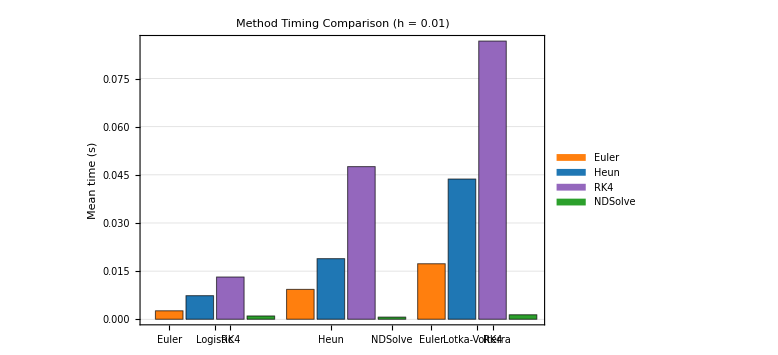

```mathematica
(*Performance check*)
(*Run each method multiple times for stable timing*)
nRuns=5;

timingLog=<|
"Euler"->Mean@Table[First@AbsoluteTiming[eulerSolve[logisticF,x0Log,tSpanLog,0.01]],nRuns],
"Heun"->Mean@Table[First@AbsoluteTiming[heunSolve[logisticF,x0Log,tSpanLog,0.01]],nRuns],
"RK4"->Mean@Table[First@AbsoluteTiming[rk4Solve[logisticF,x0Log,tSpanLog,0.01]],nRuns],
"NDSolve"->Mean@Table[First@AbsoluteTiming[
NDSolve[{x'[t]==logisticF[x[t],t],x[0]==x0Log},x,
{t,0,8},MaxStepSize->0.01]],nRuns]
|>;

timingTemp=<|
"Euler"->Mean@Table[First@AbsoluteTiming[eulerSolve[TempF, x0Temp, tSpanTemp,0.01]],nRuns],
"Heun"->Mean@Table[First@AbsoluteTiming[heunSolve[TempF, x0Temp, tSpanTemp,0.01]],nRuns],
"RK4"->Mean@Table[First@AbsoluteTiming[rk4Solve[TempF, x0Temp, tSpanTemp,0.01]],nRuns],
"NDSolve"->Mean@Table[First@AbsoluteTiming[
NDSolve[{x'[t]==TempF[x[t],t],x[0]==x0Temp},x,
{t,tSpanTemp[[1]],tSpanTemp[[2]]}]],nRuns]
|>;

timingLV=<|
"Euler"->Mean@Table[First@AbsoluteTiming[eulerSolve[lvF,xy0LV,tSpanLV,0.01]],nRuns],
"Heun"->Mean@Table[First@AbsoluteTiming[heunSolve[lvF,xy0LV,tSpanLV,0.01]],nRuns],
"RK4"->Mean@Table[First@AbsoluteTiming[rk4Solve[lvF,xy0LV,tSpanLV,0.01]],nRuns],
"NDSolve"->Mean@Table[First@AbsoluteTiming[
NDSolve[{x'[t]==α x[t]-β x[t] y[t],y'[t]==δ x[t] y[t]-γ y[t],
x[0]==xy0LV[[1]],y[0]==xy0LV[[2]]},
{x,y},{t,tSpanLV[[1]],tSpanLV[[2]]}]],nRuns]
|>;

timingBar=BarChart[
{Values[timingLog],Values[timingTemp],Values[timingLV]},
ChartLabels->{{"Logistic","Stefan's Law","Lotka-Volterra"},
{"Euler","Heun","RK4","NDSolve"}},ChartStyle->{orange,blue,purple,green},ChartLegends->{"Euler","Heun","RK4","NDSolve"},FrameLabel->{None,"Mean time (s)"},PlotLabel->Style["Method Timing Comparison (h = 0.01)",14,Bold],GridLines->{None,Automatic},Frame->True,ImageSize->Large]
```

A set of interactive plots is defined:

```mathematica
(*Logistic Equation Explorer*)
Manipulate[
  Module[{f, exact, euler,heun, rk4, nd, errE,errH, errR, tg},
    f=Function[{x, t}, r x (1 - x/K)];
    exact=Function[tt, K / (1 + ((K - x0)/x0) Exp[-r tt])];

    euler=eulerSolve[f, x0, {0.0, tMax}, h];
heun=heunSolve[f, x0, {0.0, tMax}, h];
    rk4=rk4Solve[f,   x0, {0.0, tMax}, h];

    nd=NDSolve[{xN'[t] == f[xN[t], t], xN[0] == x0},
                 xN, {t, 0, tMax}, MaxStepSize -> h];
    ndFn=xN /. nd[[1]];

    tg=euler[[All, 1]];
    errE=Max[Abs[euler[[All, 2]] - exact /@ tg]];
errH=Max[Abs[heun[[All, 2]] - exact /@ tg]];
    errR  = Max[Abs[rk4[[All, 2]]   - exact /@ tg]];

    Column[{Show[
        ListLinePlot[{euler,heun, rk4}, Joined -> True,
          PlotStyle -> {Directive[orange, Dashed, Thick],
                        Directive[blue,   Dashed, Thick],
Directive[purple,   Dashed, Thick]},
          PlotRange -> {{0, tMax}, {0, K * 1.1}},
          Frame -> True, GridLines -> Automatic,
          FrameLabel -> {"t","x(t)"},
          PlotLabel -> Style["Logistic Equation", 14, Bold],
 ImageSize->Medium
        ],
        Plot[{exact[t], ndFn[t]}, {t, 0, tMax},
          PlotStyle -> {Directive[green, Thick],
                        Directive[red, Dotted, Thick]}],
        PlotLegend -> None
      ],
      Grid[{
        {Style["Euler max|err|", Bold], ScientificForm[errE, 4]},
{Style["Heun  max|err|", Bold], ScientificForm[errH, 4]},
        {Style["RK4   max|err|", Bold], ScientificForm[errR, 4]}
      }, Frame -> All]
    }, Spacings -> 1]
  ],

  (* Controls *)
  {{r,  1.5, "Growth rate r"},   0.1, 4.0, 0.05, Appearance -> "Labeled"},
  {{K,  10.0, "Carrying cap K"}, 2.0, 20.0, 0.5,  Appearance -> "Labeled"},
  {{x0, 0.5,  "x₀"},             0.1, K-0.1, 0.1,  Appearance -> "Labeled"},
  {{h,  0.2,  "Step size h"},    0.02, 0.8, 0.02, Appearance -> "Labeled"},
  {{tMax, 8.0, "t_max"},         2.0, 20.0, 1.0,  Appearance -> "Labeled"},
  ControlPlacement -> Left,
  SaveDefinitions -> True
]
```

```mathematica
(*Stefan's Law Explorer*)
Tm=20;k=-10^-7;
Manipulate[
  Module[{f, exact, euler,heun, rk4, nd, errE,errH, errR, tg},
    f=Function[{x, t}, k(x^4-Tm^4)];

    euler=eulerSolve[f, x0, {0.0, tMax}, h];
heun=heunSolve[f, x0, {0.0, tMax}, h];
    rk4=rk4Solve[f,   x0, {0.0, tMax}, h];
(*NDSolve reference*)
    nd=NDSolve[{x'[t] == f[x[t], t], x[0] == x0},
                 x, {t, 0, tMax}];
    ndFn=x /. nd[[1]];
    tg=euler[[All, 1]];
    errE=Max[Abs[euler[[All, 2]] - ndFn /@ tg]];
errH=Max[Abs[heun[[All, 2]] - ndFn /@ tg]];
    errR  = Max[Abs[rk4[[All, 2]]   - ndFn /@ tg]];

    Column[{Show[
        ListLinePlot[{euler,heun, rk4}, Joined -> True,
          PlotStyle -> {Directive[orange, Dashed, Thick],
                        Directive[blue,   Dashed, Thick],
Directive[purple,   Dashed, Thick]},
          PlotRange -> {{-1, tMax}, {0, x0 * 1.1}},
          Frame -> True, GridLines -> Automatic,
          FrameLabel -> {"t", "T(t)"},
          PlotLabel -> Style["Stefan's Law", 14, Bold],
ImageSize->Medium
        ],
        Plot[{ndFn[t]}, {t, 0, tMax},
          PlotStyle -> {Directive[green, Thick],
                        Directive[red, Dotted, Thick]}],
        PlotLegend -> None
      ],
      Grid[{
        {Style["Euler max|err|", Bold], ScientificForm[errE, 4]},
{Style["Heun  max|err|", Bold], ScientificForm[errH, 4]},
        {Style["RK4   max|err|", Bold], ScientificForm[errR, 4]}
      }, Frame -> All]
    }, Spacings -> 1]
  ],

  (* Controls *)
  {{k,  -10^-7, "Prop. constant k"},   -10^-9,-10^-7, 10^-8, Appearance -> "Labeled"},
  {{Tm,  20.0, "Medium temp Tm"}, 0.0, 50.0, 5,  Appearance -> "Labeled"},
  {{x0, 300,  "T₀"},             100, 350, 25,  Appearance -> "Labeled"},
  {{h,  0.2,  "Step size h"},    0.02, 0.4, 0.02, Appearance -> "Labeled"},
  {{tMax, 30.0, "t_max"},         10.0, 40.0, 1.0,  Appearance -> "Labeled"},
  ControlPlacement -> Left,
  SaveDefinitions -> True
]
```

```mathematica
(*Lotka-Volterra Explorer*)
Manipulate[
  Module[{f, euler, rk4, ep, pp, rp, rpp, nd, xNDf, yNDf},
    f = Function[{xy, t},
         {a xy[[1]] - b xy[[1]] xy[[2]],
          d xy[[1]] xy[[2]] - g xy[[2]]}];

    euler = eulerSolve[f, {x0, y0}, {0.0, tEnd}, h];
    rk4   = rk4Solve[f,   {x0, y0}, {0.0, tEnd}, h];

    nd = NDSolve[{xN'[t] == a xN[t] - b xN[t] yN[t],
                  yN'[t] == d xN[t] yN[t] - g yN[t],
                  xN[0] == x0, yN[0] == y0},
                 {xN, yN}, {t, 0, tEnd}];
    {xNDf, yNDf} = {xN, yN} /. nd[[1]];

    ep  = {#[[1]], #[[2, 1]]} & /@ euler;
    pp  = {#[[1]], #[[2, 2]]} & /@ euler;
    rp  = {#[[1]], #[[2, 1]]} & /@ rk4;
    rpp = {#[[1]], #[[2, 2]]} & /@ rk4;

    GraphicsRow[{
      (* Time series *)
      Show[
        ListLinePlot[{rp, rpp},
          PlotStyle -> {Directive[blue, Thick], Directive[purple, Thick]},
          Frame -> True, GridLines -> Automatic,
          FrameLabel -> {"t", "Pop."}, PlotRange -> All,
          PlotLabel -> Style["Time Series (RK4 + NDSolve)", 12, Bold]
        ],
        Plot[{xNDf[t], yNDf[t]}, {t, 0, tEnd},
          PlotStyle -> {Directive[green, Thick], Directive[green, Dashed]}]
      ],
      (* Phase portrait *)
      Show[
        ListLinePlot[{euler[[All, 2]], rk4[[All, 2]]},
          PlotStyle -> {Directive[orange, Dashed], Directive[blue]},
          Frame -> True, FrameLabel -> {"Prey", "Pred."},
          PlotLabel -> Style["Phase Portrait", 12, Bold]
        ],
        ParametricPlot[{xNDf[t], yNDf[t]}, {t, 0, tEnd},
          PlotStyle -> Directive[green, Thick]],
        Graphics[{PointSize[0.02], red, Point[{x0, y0}]}]
      ]
    }, ImageSize -> {900, 380}]
  ],

  {{a,  1.0,  "α  prey growth"},    0.1, 3.0, 0.05, Appearance -> "Labeled"},
  {{b,  0.1,  "β  predation rate"}, 0.01, 0.5, 0.01, Appearance -> "Labeled"},
  {{d,  0.075,"δ  pred efficiency"},0.01, 0.3, 0.005,Appearance -> "Labeled"},
  {{g,  1.5,  "γ  pred death"},     0.1, 3.0, 0.05, Appearance -> "Labeled"},
  {{x0, 10.0, "Prey₀"},            1.0, 30.0, 0.5,  Appearance -> "Labeled"},
  {{y0, 5.0,  "Predator₀"},        1.0, 20.0, 0.5,  Appearance -> "Labeled"},
  {{h,  0.05, "Step size h"},      0.005, 0.2, 0.005,Appearance -> "Labeled"},
  {{tEnd, 30.0,"t_end"},           5.0, 60.0, 5.0,  Appearance -> "Labeled"},
  ControlPlacement -> Left,
  SaveDefinitions -> True
]
```